```mathematica
Item[KeyEvent["m",Modifiers->{Control}],FrontEndExecute[{FrontEnd`SelectionMove[FrontEnd`SelectedNotebook[],All,Cell],FrontEnd`FrontEndToken["Clear"]}]],
```

```mathematica
(*Let's calculate m_infinity and n_infinity*)
aM := (0.1*(25-V[t]))/(Exp[(0.1*(25-V[t]))]-1)
bM := 4*Exp[-V[t]/18]
mInf := (aM)/(aM+bM)
```

```mathematica
aN:= (0.1*(10-V[t]))/(Exp[(0.1*(10-V[t]))]-1)
```

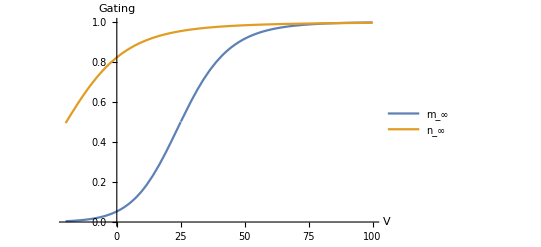

```mathematica
bN := 0.125*Exp[-V[t]/80]
nInf:= (aN)/(aN+bN)
tauN := 1/(aN+bN)
(* Now we can plot these gating variables *)

Plot[{mInf,nInf},{V[t], -20, 100}, PlotLegends->{Subscript[m, Infinity], Subscript[n, Infinity]}, AxesLabel->{V, "Gating"}]
```

```mathematica
gNa := 120
gK := 36
gL := 0.3
eNa := 115
eK := -12
eL := 10.6
```

Unset::write: Tag Function in (0&)[t] is Protected.

Unset::norep: Assignment on V for V[t] not found.

```mathematica
fastSlow=NDSolve[{V'[t]==-gNa*mInf^3(1-nn[t])(V[t]-eNa)-gK * nn[t]^4(V[t]-eK)-gL(V[t]-eL),nn'[t]==(nInf-nn[t])/(tauN),V[0]==5, nn[0]==-3},{V, nn},{t,30}]
```

{{V→InterpolatingFunction[{{0., 30.}}, <>],nn→InterpolatingFunction[{{0., 30.}}, <>]}}

```mathematica
(* Plot action potential *)
```

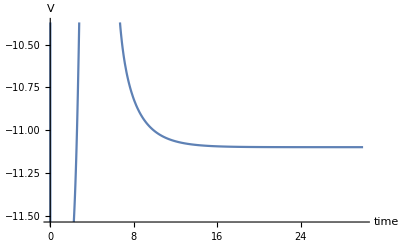

```mathematica
Plot[V[t]/.fastSlow,{t,0,30}, AxesLabel->{"time", V}]
```

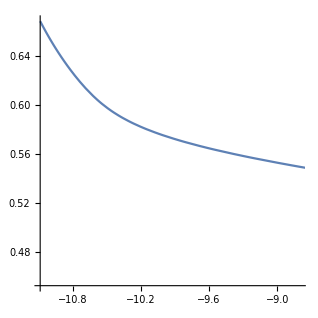

```mathematica
ParametricPlot[Evaluate[{V[t],nn[t]}/.fastSlow],{t,0,10}, AspectRatio-> 1]
```

```mathematica
(* Define null-clines of fast-slow *)
```

```mathematica
null1 := nInf - x
null2:= (100-gNa*mInf^3(1-x)(V[t]-eNa)-gK * x^4(V[t]-eK)-gL(V[t]-eL))
null2Sol:= NSolve[null2==0,V[t]]
```

```mathematica
(* Plot null-clines of fast-slow in vector field*)
(* ,Point[{x,V[t]}/.First[NSolve[{null1==0,null2==0}]]] *)
```

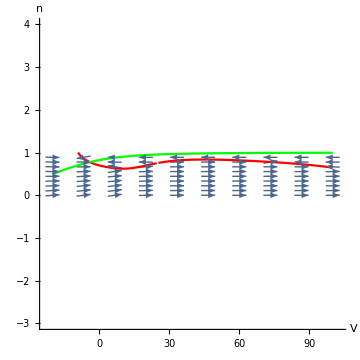

```mathematica
Show[VectorPlot[{null2,null1},{V[t],-20,100},{x,0,1},Epilog->{PointSize[0.03]},Frame->False,Axes->True,VectorScale->{0.05,0.1,None},VectorPoints->Coarse,ImageSize->Medium],ContourPlot[{null2==0,null1==0},{V[t],-20,100},{x,0,1},ContourStyle->{Red, Green}], AxesLabel-> {V, n}]
```

```mathematica
Export["/Users/farissbahi/Desktop/PHY513/PHY 513 - Final Project/fast_slow_nullclines_iext.png",%167,"PNG"]
```

/Users/farissbahi/Desktop/PHY513/PHY 513 - Final Project/fast_slow_nullclines_iext.png

```mathematica
Export["/Users/farissbahi/Desktop/PHY513/PHY 513 - Final Project/fast_slow_nullclines.png",%101,"PNG"]
```

/Users/farissbahi/Desktop/PHY513/PHY 513 - Final Project/fast_slow_nullclines.png